{{3.94151×10^-10,6.24754×10^-10},{4.42149×10^-10,3.7905×10^-10},{8.13665×10^-10,9.59055×10^-10},{8.5682×10^-10,7.17506×10^-10},{1.39949×10^-9,1.62773×10^-9},{1.43678×10^-9,1.3864×10^-9},{2.22524×10^-9,2.78272×10^-9},{2.25032×10^-9,2.43047×10^-9},{2.47524×10^-9,2.78272×10^-9},{2.50032×10^-9,2.43047×10^-9},{2.72524×10^-9,2.78272×10^-9},{2.75032×10^-9,2.43047×10^-9},{2.97524×10^-9,2.78272×10^-9},{3.00032×10^-9,2.43047×10^-9},{3.22524×10^-9,2.78272×10^-9},{3.25032×10^-9,2.43047×10^-9},{3.47524×10^-9,2.78272×10^-9},{3.50032×10^-9,2.43047×10^-9},{3.72524×10^-9,2.78272×10^-9},{3.75032×10^-9,2.43047×10^-9},{3.97524×10^-9,2.78272×10^-9},{4.00032×10^-9,2.43047×10^-9},{4.22524×10^-9,2.78272×10^-9},{4.25032×10^-9,2.43047×10^-9},{4.47524×10^-9,2.78272×10^-9},{4.50032×10^-9,2.43047×10^-9},{4.72524×10^-9,2.78272×10^-9},{4.75032×10^-9,2.43047×10^-9},{4.97524×10^-9,2.78272×10^-9}}

ParametricPlot::sclfn: -- Message text not found -- ({{#1/1000000000&,1000000000 #1&},{#1/1000000000&,1000000000 #1&}})

ParametricPlot::sclfn: -- Message text not found -- ({{#1/1000000000&,1000000000 #1&},{#1/10000000000&,10000000000 #1&}})

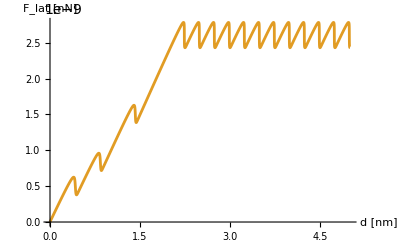
-Graphics-1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(1-Cos[c7 2Pi(x[t])/a])+c3 q[t]^4

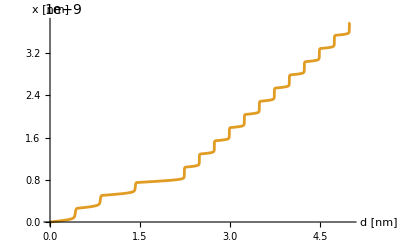
-Graphics-1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(1-Cos[c7 2Pi(x[t])/a])+c3 q[t]^4

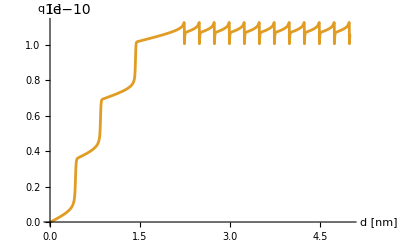
-Graphics-1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(1-Cos[c7 2Pi(x[t])/a])+c3 q[t]^4

```mathematica
(*main program, making plots for fric, x, q*)


Needs["DifferentialEquations`NDSolveUtilities`"];

SetDirectory["/home/storluffarn/phd-stuff/research/graphene/images/"];

(*reference values*)

(* single slip*)
(*
c11=4.0*^-20;
c22=3.0;
ηn=5.0*^12;

k = 2.0; (*Li: 0.8*)
v = 1; (*Li: *2*)
v2=0.5;
c1=c11; (*Li: ~9*^-17?!*)
c2=c22;
c3=14*^20; (*3.5*^1 for q^2*)
c4=7.0; (*period is ~99.5?*)
c5=0.5c11; (* 2.5*^-21 *)
c6=0.5c22; (* 1 *)
c7=1.0; (*period is ~7.1072?*)
a = 2.5*^-10; (*Li: 2.5*^-10*)
mx = 1*^-23;
mq = 5*^-22;
ηx=1.25ηn;
ηq=ηn;
ζx=0*^-2; 
ζq=75.0*^21;
h = 1*^-15;
tmax=5000000h;
*)

(* vel dep *)
(*
c11=1.3*^-20;
c22=0.2;
ηn=3.0*^12;

k = 1.0; (*Li: 0.8*)
v = 1; (*Li: *2*)
v2=0.5;
c1=c11; (*Li: ~9*^-17?!*)
c2=c22;
c3=8*^18; (*1.0*^0 for q^2*)
c4=1.0; (*period is ~99.5?*)
c5=0.0c11; (* 2.5*^-21 *)
c6=0.0c22; (* 1 *)
c7=1.0; (*period is ~7.1072?*)
a = 2.5*^-10; (*Li: 2.5*^-10*)
mx = 1*^-23;
mq = 5*^-22;
ηx=1.25ηn;
ηq=ηn;
ζx=0*^-2; 
ζq=0.0*^21;
h = 1*^-15;
tmax=7500000h;
*)

(*parameter values*)

c11=4.0*^-20;
c22=3.0;
ηn=5.0*^12;

k = 2.0; (*Li: 0.8*)
v = 1; (*Li: *2*)
v2=0.5;
c1=c11; (*Li: ~9*^-17?!*)
c2=c22;
c3=14*^20; (*3.5*^1 for q^2*)
c4=7.0; (*period is ~99.5?*)
c5=0.5c11; (* 2.5*^-21 *)
c6=0.5c22; (* 1 *)
c7=1.0; (*period is ~7.1072?*)
a = 2.5*^-10; (*Li: 2.5*^-10*)
mx = 1*^-23;
mq = 5*^-22;
ηx=1.25ηn;
ηq=ηn;
ζx=0*^-2; 
ζq=75.0*^21;
h = 1*^-15;
tmax=5000000h;

(*with gaussians*)

(*
scale=2.5*^-10; (* 1.5*^-10 and 50 for even grid *)
terms=20;
μ=a/5;

(*σ=Table[RandomReal[{0,1*^-8}],{n,1,terms}];
clist=Table[n,{n,1,terms}]-0.5;
clist*=1*^-8/terms;
N@clist;
norms=scale Sum[PDF[NormalDistribution[σ[[n]],μ],x],{n,1,Length@σ}];*)

σ=RandomVariate[NormalDistribution[0,μ],terms];
clist=Table[n,{n,1,terms}]-0.5;
clist*=tmax/terms;
clist+=0.5*σ;

norms=scale Sum[PDF[NormalDistribution[clist[[n]],μ],x],{n,1,Length@clist}];

Plot[norms,{x,0,1*^-9},PlotRange->All,PlotLabel->"grid"]
Plot[norms,{x,0,tmax},PlotRange->All,PlotLabel->"grid"]
Plot[(1-Cos[c7 2Pi(x)/a]),{x,0,1*^-9},PlotLabel->"original grid"]

anpotstring="1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(scale Sum[PDF[NormalDistribution[clist[[n]],μ],x[t]],{n,1,Length@clist}])+c3 q[t]^4";
anpot=ToExpression[anpotstring];
anpotstring2="1/2k(x[t]-v2 t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(scale Sum[PDF[NormalDistribution[clist[[n]],μ],x[t]],{n,1,Length@clist}])+c3 q[t]^4";
anpot2=ToExpression[anpotstring2];
*)

(*with sines*)
(*
s1=8*^-0;
s2=2.5*^10;
a1=0.1;
a3=0.025;
p1=1;
p2=2;
p3=5;
num=1;
lim=2;
terms=10;
r=Table[RandomReal[{-num,num}],{t,0,100}];
fun[t_]:=s1 a3 Sum[r[[2i+1]]Cos[s2 p1 r[[2i+1+1]] t],{i,0,terms-1}]+
s1 a2 Sum[r[[2i+1]]Cos[s2 p2 r[[2i+1+1]] t],{i,terms,2terms-1}]+
s1 a1 Sum[r[[2i+1]]Cos[s2 p3 r[[2i+1+1]] t],{i,2terms,2terms-1}];
Plot[fun[t]+Abs[fun[0]],{t,0,1*^-9},PlotRange->All]
Plot[fun[t]+Abs[fun[0]],{t,0,1*^-8},PlotRange->All]

anpotstring="1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(fun[x[t]]+Abs[fun[0]])+c3 q[t]^2";
anpot=ToExpression[anpotstring];

*)

(*potential to be used*)

anpotstring=
"1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(1-Cos[c7 2Pi(x[t])/a])+c3 q[t]^4";
anpot=ToExpression[anpotstring];
anpotstring2=
"1/2k(x[t]-v2 t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+(c5+c6 q[t]^2)(1-Cos[c7 2Pi(x[t])/a])+c3 q[t]^4";
anpot2=ToExpression[anpotstring2];

-N@D[anpot,x[t]];
-N@D[anpot,q[t]];
	
(*diff solver, stiffness switching is good for numerically striff stiff problems*)
s=NDSolve[{-mx x''[t]-D[anpot,x[t]]-mx ηx (x'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])-mq ζq q[t]==0,x[0]==0,x'[0]==0,q[0]==0,q'[0]==0},{x[t],q[t]},{t,0,tmax},MaxSteps->100000];
(*,Method->{"StiffnessSwitching"}, AccuracyGoal->∞, "TimeIntegration"-> *)
s2=NDSolve[{-mx x''[t]-D[anpot2,x[t]]-mx ηx (x'[t])==0,-mq q''[t]-D[anpot2,q[t]]-mq ηq(q'[t])-mq ζq q[t]==0,x[0]==0,x'[0]==0,q[0]==0,q'[0]==0},{x[t],q[t]},{t,0,tmax*v/v2},MaxSteps->100000];

(*extract the extrema*)
extrema=Reap[k(v t-x[t]/.First[NDSolve[{-mx x''[t]-D[anpot,x[t]]-mx ηx (x'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])-mq ζq q[t]==0,x[0]==0,x'[0]==0,q[0]==0,q'[0]==0},{x,q},{t,0,tmax},Method->{"EventLocator","Event"->D[k(v t-x[t]),t],"EventAction":>Sow[{t,k(v t-x[t])}]},MaxSteps->100000]])][[2,1]];qextrema=Reap[k(q/.First[NDSolve[{-mx x''[t]-D[anpot,x[t]]-mx ηx (x'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])-mq ζq q[t]==0,x[0]==0,x'[0]==0,q[0]==0,q'[0]==0},{x,q},{t,0,tmax},Method->{"EventLocator","Event"->D[q[t],t],"EventAction":>Sow[{t,q[t]}]},MaxSteps->100000]])][[2,1]];
extrema={v#[[1]],#[[2]]}&/@extrema
extremaq={v#[[1]],#[[2]]}&/@extrema;

(*this is for curve fitting to maxima, to find the slope*)
maxdiff=Max[Table[extrema[[i+2]][[2]]-extrema[[i]][[2]],{i,1,Length[extrema]-2}]];
tol= maxdiff-0.45maxdiff;
fitdata=Table[If[extrema[[i+2]][[2]]-extrema[[i]][[2]]>tol,extrema[[i]],##&[]],{i,1,Length[extrema]-2}];
fit=LinearModelFit[fitdata,t,t];
(*fitplot=Plot[fit[x],{x,0,tmax},PlotStyle->{Red,Dashed}];*)
fitplot=ParametricPlot[{t,fit[t]},{t,0,v tmax/2},PlotStyle->Directive[Thickness[0.003],Red,Dashed]];
(*rescale slope*)
(*fitdata[[All,1]]*=v
fit=LinearModelFit[fitdata,t,t];*)
flatfitdata=Table[extrema[[2i-2]],{i,Length[extrema]/2-4,Length[extrema]/2}];
flatfit=LinearModelFit[flatfitdata,t,t];
flatfitplot=Plot[flatfit[x],{x,0,tmax},PlotStyle->{Dashed,Red}];

(*make plot*)
xmaxv=tmax;
qmaxv=2*^-10;
glinesx=Table[i,{i,0,xmaxv,a}];
glinesq=Table[i,{i,0,qmaxv,qmaxv/20}];
fricimg=ParametricPlot[{v t,k(v t-Evaluate[x[t]/.s])},{t,0,tmax},PlotPoints->300,PlotRange->All,AspectRatio->1/GoldenRatio,AxesLabel->{"d [nm]","F_lat [nN]"},PlotStyle->Thickness[0.005],LabelStyle->FontSize->12,ScalingFunctions->{{1*^-9#&,1*^9#&},{1*^-9#&,1*^9#&}}];
fricimg2=ParametricPlot[{v2 t,k(v2 t-Evaluate[x[t]/.s2])},{t,0,tmax*v/v2},PlotPoints->300,PlotRange->All,AspectRatio->1/GoldenRatio,AxesLabel->{"d [nm]","F_lat [nN]"},PlotStyle->Directive[Gray,Thickness[0.005],Dashed],LabelStyle->FontSize->12,ScalingFunctions->{{1*^-9#&,1*^9#&},{1*^-9#&,1*^9#&}}];
(*,Epilog->{Red,Point[extrema]},LabelStyle->FontSize->15,
PlotStyle->Directive[Gray,Thickness[0.005]],
PlotStyle->Directive[Thickness[0.003],Dashing[Medium]]*)

xmaxv=tmax;
qmaxv=2*^-10;
glinesx=Table[i,{i,0,xmaxv,a}];
glinesq=Table[i,{i,0,qmaxv,qmaxv/20}];
ximg = ParametricPlot[{v t,Evaluate[x[t]/.s]},{t,0,tmax},PlotPoints->500,PlotRange->Automatic,AspectRatio->1/GoldenRatio,AxesLabel->{"d [nm]","x [nm]"},PlotStyle->Thickness[0.005],LabelStyle->FontSize->12,ScalingFunctions->{{1*^-9#&,1*^9#&},{1*^-9#&,1*^9#&}}];

xmaxv=tmax;
qmaxv=2*^-10;
glinesx=Table[i,{i,0,xmaxv,a}];
glinesq=Table[i,{i,0,qmaxv,qmaxv/20}];
qimg = ParametricPlot[{v t,Evaluate[q[t]/.s]},{t,0,tmax},PlotPoints->500,PlotRange->Automatic,AspectRatio->1/GoldenRatio,AxesLabel->{"d [nm]","q [.]"},PlotStyle->Thickness[0.005],PlotStyle->Thickness[0.005],LabelStyle->FontSize->12,ScalingFunctions->{{1*^-9#&,1*^9#&},{1*^-10#&,1*^10#&}}];
(*GridLines->{glinesx, Automatic},*)
(*qimg=ParametricPlot[{v t,Evaluate[q[t]/.s]},{t,0,tmax},PlotPoints->500,PlotRange->All,
ImageSize->800,AspectRatio->1/GoldenRatio,AxesLabel->{"distance","q[t]"},Epilog->{Red,Point[qextrema]}];*)
(*,PlotStyle->Thickness[0.005]*)

StepDataPlot[s];

(*add legend*)
ximg=Labeled[Legended[Show[ximg],Column[{StringForm["k: ``",N@k],StringForm["v: ``",N@v],StringForm["v2: ``",N@v2],StringForm["c1: ``",N@c1],StringForm["c2: ``",N@c2],StringForm["c3: ``",N@c3],StringForm["c4: ``",N@c4],StringForm["c5: ``",N@c5],StringForm["c6: ``",N@c6],StringForm["c7: ``",N@c7],StringForm["a: ``",N@a],StringForm["mx: ``",N@mx],StringForm["mq: ``",N@mq],StringForm["η_x: ``",N@ηx],StringForm["η_q: ``",N@ηq],StringForm["ζ_q: ``",N@ζq],StringForm["timestep: ``",N@h],StringForm["runtime: ``",N@tmax]}]],anpotstring,{Top}];

qimg=Labeled[Legended[Show[qimg],Column[{StringForm["k: ``",N@k],StringForm["v: ``",N@v],StringForm["v2: ``",N@v2],StringForm["c1: ``",N@c1],StringForm["c2: ``",N@c2],StringForm["c3: ``",N@c3],StringForm["c4: ``",N@c4],StringForm["c5: ``",N@c5],StringForm["c6: ``",N@c6],StringForm["c7: ``",N@c7],StringForm["a: ``",N@a],StringForm["mx: ``",N@mx],StringForm["mq: ``",N@mq],StringForm["η_x: ``",N@ηx],StringForm["η_q: ``",N@ηq],StringForm["ζ_q: ``",N@ζq],StringForm["timestep: ``",N@h],StringForm["runtime: ``",N@tmax]}]],anpotstring,{Top}];

fricimg=Labeled[Legended[Show[fricimg],Column[{StringForm["k: ``",N@k],StringForm["v: ``",N@v],StringForm["v2: ``",N@v2],StringForm["c1: ``",N@c1],StringForm["c2: ``",N@c2],StringForm["c3: ``",N@c3],StringForm["c4: ``",N@c4],StringForm["c5: ``",N@c5],StringForm["c6: ``",N@c6],StringForm["c7: ``",N@c7],StringForm["a: ``",N@a],StringForm["mx: ``",N@mx],StringForm["mq: ``",N@mq],StringForm["η_x: ``",N@ηx],StringForm["η_q: ``",N@ηq],StringForm["ζ_q: ``",N@ζq],StringForm["slope: ``" ,Normal@fit],StringForm["timestep: ``",N@h],StringForm["runtime: ``",N@tmax]}]],anpotstring,{Top}];

(*,Epilog->Inset[Column[{LineLegend[{Sunrise},{"v = 1"}],LineLegend[{Gray},{"v = 2"}]}],Scaled[{0.8,0.20}]]*)
(*fricimgtmp=fricimg;
Ticks->{Charting`ScaledTicks[{10^-9 #&,#/10^-9&}],Charting`ScaledTicks[{10^-9 #&,#/10^-9&}]}*)

(*save plots*)
fricfilename="fimage"<>ToString[UnixTime[]]<>".svg";
xfilename="ximage"<>ToString[UnixTime[]+1]<>".png";
qfilename="qimage"<>ToString[UnixTime[]+2]<>".png";
fricimg=Show[fricimg]
ximg=Show[ximg]
qimg=Show[qimg]
Export[fricfilename,fricimg];
Export[xfilename,ximg];
Export[qfilename,qimg];
(*,ImageSize->300,ImageResolution->100*)
(*,Background->RGBColor["#eaf6fe"]*)
(*,Background->None*)


(* density plots *)
(*
(*scale = 1*^18;
c1*=scale;
c2*=scale;
c3*=scale;
c4*=1;
c5*=scale;
c6*=scale;
c7*=1;*)

xmaxv=3*^-9;
qmaxv=1.5*^-10;
glinesx=Table[i,{i,0,xmaxv,a}];
glinesq=Table[i,{i,0,qmaxv,qmaxv/20}];
xticks={0,2.0*^-9,4.0*^-9,6.0*^-9};
qticks={0,0.5*^-10,1.0*^-10,1.5*^-10,2.0*^-10,2.5*^-10,3.0*^-10,3.5*^-10};

(*cont=DensityPlot[(c1+c2 q^2)(1-Cos[2Pi(x-c4 q)/a])+(c5+c6 q^2)(1-Cos[c7 2Pi(x)/a])+c3 q^4,{x,0*^-8,xmaxv},{q,0*^-9,qmaxv},PlotPoints->200,FrameLabel->{"x[t]","q[t]"},ImageSize->300,Lab*elStyle->FontSize->12,PlotLegends->Automatic];*)

(*WARNING RESCALED*)
cont=DensityPlot[Rescale[(c1+c2 q^2)(1-Cos[2Pi(x-c4 q)/a])+(c5+c6 q^2)(1-Cos[c7 2Pi(x)/a])+0*c3 q^4,{0,1*^-18},{0,1}],{x,0*^-8,xmaxv},{q,0*^-9,qmaxv},PlotPoints->200,FrameLabel->{"x [nm]","q [.]"},LabelStyle->FontSize->12,PlotLegends->Automatic];

(*GridLinesStyle->Directive[GrayLevel[0.4]],PlotLegends->Automatic,GridLines->{glinesx,glinesq},Method->{"GridLinesInFront"->True},GridLinesStyle->Directive[Gray]],FrameTicks->{{qticks,Automatic},{xticks,Automatic}},
Ticks->{Charting`ScaledTicks[{10^-9 #&,#/10^-9&}],Charting`ScaledTicks[{10^-9 #&,#/10^-9&}]},ScalingFunctions->{{1*^-9#&,1*^9#&},{1*^-9#&,1*^9#&}}*)
path=ParametricPlot[Evaluate[{x[t],q[t]}]/.s,{t,0,0.8tmax},PlotStyle->{Thickness[0.005],Red},PlotPoints->Automatic,Ticks->None];
(*path2=ParametricPlot[Evaluate[{p[t],q[t]}]/.s,{t,0,tmax},PlotStyle->{Thickness[0.005],Blue},PlotPoints->300,ImageSize->800];*)
(*path3=ParametricPlot[Evaluate[{p[t],q[t]}]/.s,{t,0,tmax},PlotStyle->{Thickness[0.005],Green},PlotPoints->300,ImageSize->800];*)
(*fig=Show[cont,path1,path2,path3]
fig=Show[cont,path2,path3]*)
fig=Show[{cont,path},FrameTicks->{{Charting`ScaledTicks[{10^-9#&,#/10^-9&}],Automatic},{Charting`ScaledTicks[{10^-9 #&,#/10^-9&}],Automatic}}]
figfilename="potland"<>ToString[UnixTime[]]<>".eps";
Export[figfilename,fig,"AllowRasterization"->True,ImageSize->300,ImageResolution->600];
*)
```

```mathematica
bot = 0.1;
top = 10;

Manipulate[DensityPlot[(c11+c22 q^2)(1-Cos[2Pi(x-c44 q)/a])+(c55+c66 q^2)(1-Cos[c77 2Pi(x)/a])+c33 q^2,{x,0*^-8,7.0*^-9},{q,0*^-9,3.0*^-10},FrameLabel->{"x[t]","q[t]"},PlotLegends->Automatic,ImageSize->600,LabelStyle->FontSize->15,PlotPoints->200],{{c11,c1},bot c1,top c1},{{c22,c2},bot c2,top c2},{{c33,c3},bot c3,top c3},{{c44,c4},bot c4,top/2 c4},{{c55,c5},bot c5,top c5},{{c66,c6},bot c6,top c6
},{{c77,c7},0,10}]
```

```mathematica
bot = 0.1;
top = 2;
step=0.1;
anime=Table[DensityPlot[(c11+c2 q^2)(1-Cos[2Pi(x-c4 q)/a])+(c5+c6 q^2)(1-Cos[c7 2Pi(x)/a])+c3 q^2,{x,0*^-8,5.0*^-9},{q,0*^-9,5*^-10},FrameLabel->{"x[t]","q[t]"},PlotLegends->Automatic,ImageSize->600,LabelStyle->FontSize->15,PlotPoints->200],{c11,c1 bot,c1 top,c1 step}];
anime=Map[Image,anime];
ListAnimate[anime]
Export["c1.avi",anime]
```

$Aborted

ListAnimate[anime]

Export::errelem: The Export element GraphicsList contains a malformed data structure and could not be exported to AVI format.

$Failed

```mathematica
Manipulate[x,{{x,1},0.1,10,Row[{Slider[Dynamic[Exp[#],(x=Log[#])&],Exp[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

```mathematica
tmp1=ximg;
tmp2=qimg;
tmp3=fricimg;
```

```mathematica
ClearAll["Global`*"]
(*potential to be used*)
aanpotstring="1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+c3 q[t]^4";
aanpot=ToExpression[aanpotstring];

D[aanpot,x[t]]
D[aanpot,q[t]]
```

```mathematica
FullForm@ColorData[97,#]&/@Range[Length@ColorData[97,"ColorList"]]//TableForm
```

RGBColor[0.368417,0.506779,0.709798]
RGBColor[0.880722,0.611041,0.142051]
RGBColor[0.560181,0.691569,0.194885]
RGBColor[0.922526,0.385626,0.209179]
RGBColor[0.528488,0.470624,0.701351]
RGBColor[0.772079,0.431554,0.102387]
RGBColor[0.363898,0.618501,0.782349]
RGBColor[1,0.75,0]
RGBColor[0.647624,0.37816,0.614037]
RGBColor[0.571589,0.586483,0.]
RGBColor[0.915,0.3325,0.2125]
RGBColor[0.400822,0.522007,0.85]
RGBColor[0.972829,0.621644,0.073362]
RGBColor[0.736783,0.358,0.503027]
RGBColor[0.280264,0.715,0.429209]

```mathematica
RGBColor[0.880722,0.611041,0.142051]
```

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
temp = 300;
ξx=1*^20;
ξq=1*^-5;
kB=1.38064852*^-23;

σx=Sqrt[2ξx mx kB temp];
(*potential to be used*)
anpotstring="1/2k(x[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(x[t]-c4 q[t])/a])+c3 q[t]^4";
anpot=ToExpression[anpotstring];

-N@D[anpot,x[t]];
-N@D[anpot,q[t]];

(*diff solver, stiffness switching is good for numerically striff stiff problems*)
s=NDSolve[{-mx x''[t]-D[anpot,x[t]]-mx ηx (x'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])==0,x[0]==0,x'[0]==0,q[0]==0,q'[0]==0},{x[t],q[t]},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}] (*,Method->{"StiffnessSwitching"} AccuracyGoal->∞, "TimeIntegration"-> *)
```

```mathematica
cont=ContourPlot[(c1+c2 q^2)(1-Cos[2Pi(x-c4 q)/a])+(c5+c6 q^2)(1-Cos[1.15*2Pi(x)/a])+c3 q^2,{x,0*^-8,7.0*^-9},{q,0*^-9,3.0*^-10},PlotPoints->100,FrameLabel->{"x[t]","q[t]"},PlotLegends->Automatic,ImageSize->800,LabelStyle->FontSize->15]
```

```mathematica
Clear["Global`*"]
```

{{x[t]→InterpolatingFunction[{{0., 20.}}, <>][t],y[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

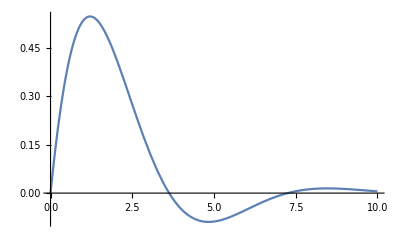

```mathematica
s=NDSolve[{x''[t]+y'[t]+x[t]==0,y''[t]+x'[t]+y[t]==0,x[0]==0,y[0]==0,x'[0]==1,y'[0]==1},{x[t],y[t]},{t,0,tmax}]
pl1=Plot[Evaluate@x[t]/.s,{t,0,10},PlotRange->All]
```

{{x[t]→InterpolatingFunction[{{0., 10.}}, <>][t],y[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

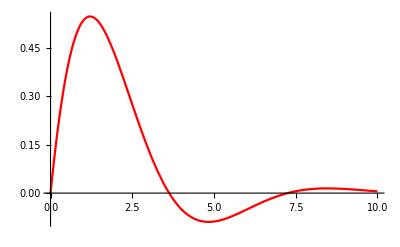

ItoProcess[{{0.+1. xx[t],0.+1. (-1. x[t]-1. yy[t]),0.+1. yy[t],0.+1. (-1. xx[t]-1. y[t])},{{0.,0.},{0.001,0.},{0.,0.},{0.,0.001}},{x[t],xx[t],y[t],yy[t]}},{{x,xx,y,yy},{0,1,0,1}},{t,0}]

TemporalData[…]

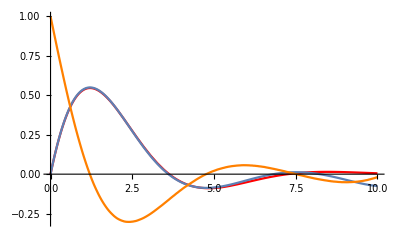

```mathematica
(*tmax=10;
ξ=0.1;
s=NDSolve[{x''[t]+Sin[x[t]]+0.5x'[t]==0,x[0]==1,x'[0]==0},{x[t],y[t]},{t,0,tmax}]
pl1=Plot[Evaluate@x[t]/.s,{t,0,tmax},PlotRange->All,PlotStyle->Red];
s=ItoProcess[{ⅆx[t]==ⅆt xx[t],ⅆxx[t]==ⅆt(-Sin[x[t]]-0.5xx[t])+ξⅆnoise[t]},{x[t],xx[t]},{{x,xx},{1,0}},{t,0},noise\[Distributed]WienerProcess[0,1]]
RandomFunction[s,{0,tmax,0.01}];
pl2=ListLinePlot[%];
Show[pl1,pl2]*)


tmax=10;
ξx=0.001;
ξy=0.001;
s=NDSolve[{x''[t]+y'[t]+x[t]==0,y''[t]+x'[t]+y[t]==0,x[0]==0,y[0]==0,x'[0]==1,y'[0]==1},{x[t],y[t]},{t,0,tmax}]
pl1a=Plot[Evaluate@x[t]/.s,{t,0,tmax},PlotRange->All,PlotStyle->Red,PlotRange->All]
pl1b=Plot[Evaluate@y[t]/.s,{t,0,tmax},PlotRange->All];
s=ItoProcess[{ⅆx[t]==ⅆt xx[t],ⅆy[t]==ⅆt yy[t],ⅆxx[t]==ⅆt(-yy[t]-x[t])+ξxⅆxnoise[t],ⅆyy[t]==ⅆt(-xx[t]-y[t])+ξyⅆynoise[t]},{x[t],xx[t],y[t],yy[t]},{{x,xx,y,yy},{0,1,0,1}},{t,0},{xnoise\[Distributed]WienerProcess[0,1],ynoise\[Distributed]WienerProcess[0,1]}]
randsamp=RandomFunction[s,{0,tmax,0.01}]
ListLinePlot[%];
pl2a=ListLinePlot[#2[[1]]&@@@randsamp["Paths"][[1]],DataRange->{0,tmax},PlotRange->All];
pl2b=ListLinePlot[#2[[2]]&@@@randsamp["Paths"][[1]],DataRange->{0,tmax},PlotStyle->Orange,PlotRange->All];
Show[pl1a,pl2a,pl2b]
```

TemporalData[…]

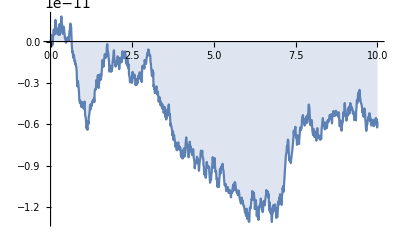

TemporalData[…]

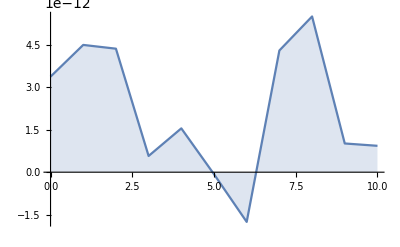

```mathematica
data=RandomFunction[WienerProcess[0,σx],{0,10,0.01}]
ListLinePlot[%,Filling->Axis]
data=RandomFunction[WhiteNoiseProcess[σx],{0,10}]
ListLinePlot[%,Filling->Axis]
```

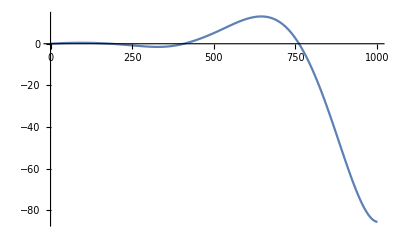

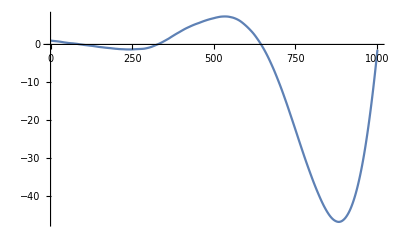

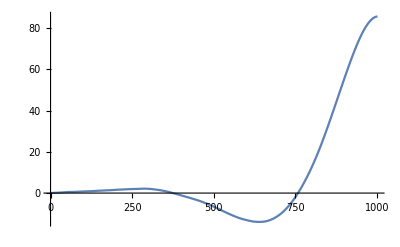

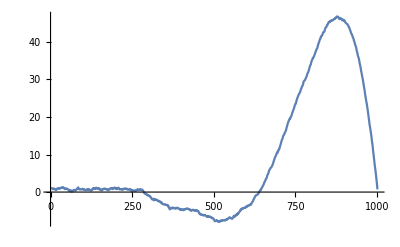

```mathematica
t1=#1&@@@randsamp["Paths"][[1]];
t2=#2[[1]]&@@@randsamp["Paths"][[1]];
t3=#2[[2]]&@@@randsamp["Paths"][[1]];
t4=#2[[3]]&@@@randsamp["Paths"][[1]];
t5=#2[[4]]&@@@randsamp["Paths"][[1]];
ListLinePlot[t2]
ListLinePlot[t3]
ListLinePlot[t4]
ListLinePlot[t5]
```

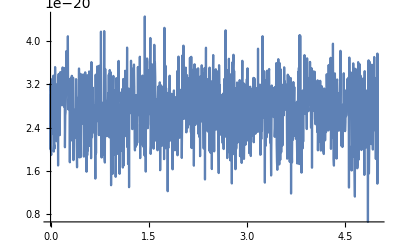

```mathematica
(*naive noise*)

s1=0.05;
s2=0.035;
s3=0.025;

phscale=4*^9;
p1=1phscale;
p2=2phscale;
p3=5phscale;
num=1;
lim=2;
terms=7;

enscale=1*^-19;
r=Table[RandomReal[{-num,num}],{t,0,100}];
ϵ[t_]:=t;
n[ϵ[t_]]:=enscale(Sum[0.01 RandomReal[n] Cos[n t/10],{n,10}])
Plot[n[ϵ[t]],{t,0,5*^-9},PlotRange->All,PlotPoints->1000]
```

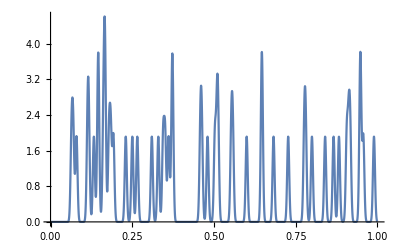

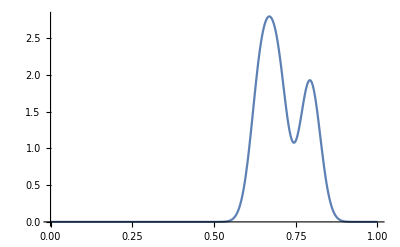

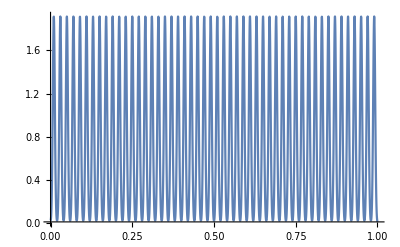

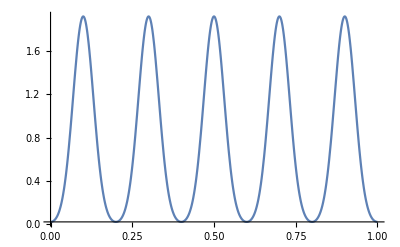

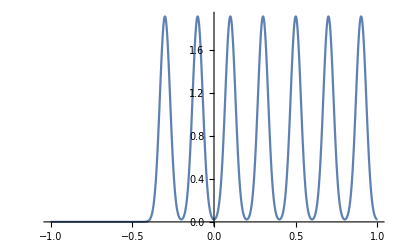

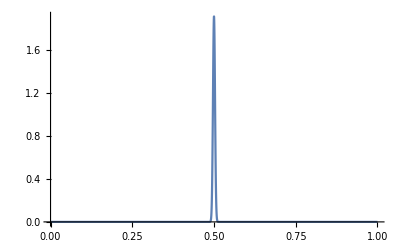

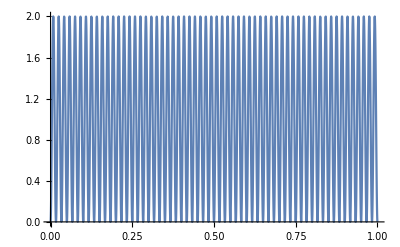

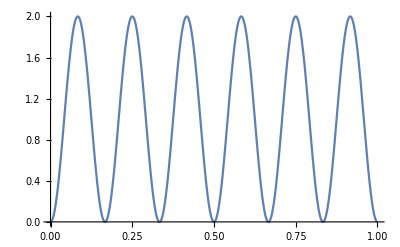

```mathematica
(*naive noise test*)

(*
(*with sines*)
s1=1*^-8;
s2=2*^10;

(*f[t_]:=Exp[-Abs[t]] Sin[t];*)
f[t_]:=0;
Plot[f[t],{t,-10,10},PlotRange->All]
(*Plot[f[t]+Sum[.01 RandomReal[n] Cos[n t/10],{n,10}],{t,-10,10},PlotRange->All]*)
a1=0.1;
a2=0.05;
a3=0.025;
p1=1;
p2=2;
p3=5;
num=1;
lim=2;
terms=10;
r=Table[RandomReal[{-num,num}],{t,0,100}];
n[t_]:=s1 a3 Sum[r[[2i+1]]Cos[s2 p1 r[[2i+1+1]] t],{i,0,terms-1}]+
s1 a2 Sum[r[[2i+1]]Cos[s2 p2 r[[2i+1+1]] t],{i,terms,2terms-1}]+
s1 a1 Sum[r[[2i+1]]Cos[s2 p3 r[[2i+1+1]] t],{i,2terms,2terms-1}];
Plot[n[t],{t,0,1*^-9},PlotRange->All]
Plot[f[t]+n[t]+Abs[n[0]],{t,0,1*^-9},PlotRange->All]
*)

(*with gaussians*)
scale=1.5*^-10;
terms=50;
μ=a/8;

σ=Table[RandomReal[{0,1*^-8}],{n,1,terms}];
clist=Table[n,{n,-1,terms}]-0.5;
clist*=1*^-8/terms;
N@clist;

norms=scale Sum[PDF[NormalDistribution[σ[[n]],μ],x],{n,1,Length@σ}];
norms2=scale Sum[PDF[NormalDistribution[clist[[n]],μ],x],{n,1,Length@clist}];
norms3=scale PDF[NormalDistribution[5*^-9,μ],x];

(*norms=scale Sum[1/Sqrt[2Pi σ[[n]]^2]Exp[-(x-μ)^2/(2σ[[n]]^2)],{n,1,Length@σ}];
norms=scale Sum[1/Sqrt[2Pi σ[[n]]^2]Exp[-(x-μ)^2/(2σ[[n]]^2)],{n,1,Length@σ}];
Plot[norms,{x,0,1*^-8},PlotRange->All];*)

Plot[norms,{x,0,1*^-8},PlotRange->All]
Plot[norms,{x,0,1*^-9},PlotRange->All]

Plot[norms2,{x,0,1*^-8},PlotRange->All]
Plot[norms2,{x,0,1*^-9},PlotRange->All]
Plot[norms2,{x,-1*^-9,1*^-9},PlotRange->All]

Plot[norms3,{x,0*^-9,1*^-8},PlotRange->All]

Plot[(1-Cos[c7 2Pi(x)/a]),{x,0,1*^-8}]
Plot[(1-Cos[c7 2Pi(x)/a]),{x,0,1*^-9}]
```

1.27662×10^10 ⅇ^(-5.12×10^20 (-1/200000000+x)^2)

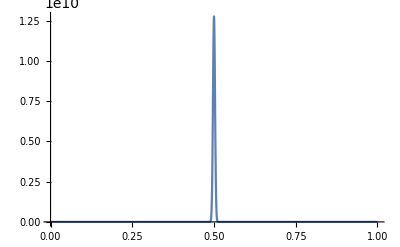

```mathematica
norms3=PDF[NormalDistribution[5*^-9,μ],x]
Plot[norms3,{x,0*^-9,1*^-8},PlotRange->All]
```

```mathematica
Sum[PDF[NormalDistribution[rands[[n]],0.5*^-9],x[t]],{}]
```

```mathematica
(*extracting iterpolated functions*)
s1=First[q/.NDSolve[{-mp p''[t]-D[anpot,p[t]]-mp ηp (p'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p,q},{t,0,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}] (*,Method->{"StiffnessSwitching"} AccuracyGoal->∞, "TimeIntegration"-> *)]
extrema;
Integrate[s1[t],{t,extrema[[Length@extrema-2]][[1]],extrema[[Length@extrema]][[1]]}]
(extrema[[Length@extrema]][[1]]-extrema[[Length@extrema-1]][[1]])/2+extrema[[Length@extrema-1]][[1]]
s1[3.0*^-9]
```

-9
InterpolatingFunction[{{0., 5. 10  }}, <>]

6.18456×10^-20

4.87386×10^-9

2.51054×10^-10

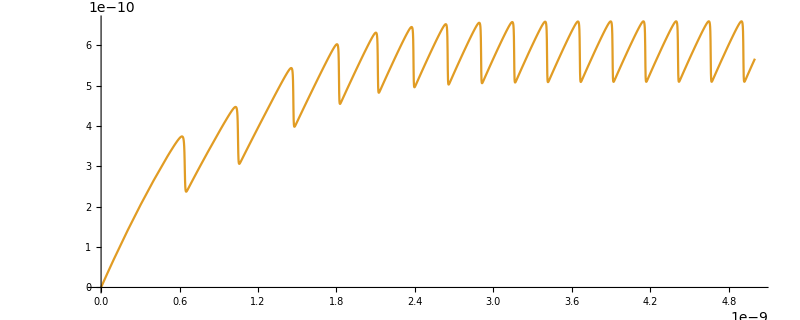

```mathematica
(*parametric plots*)

extrema
{2#[[1]],#[[2]]}&/@extrema

ParametricPlot[{v t,k(v t-Evaluate[p[t]/.s])},{t,0,tmax}]
```

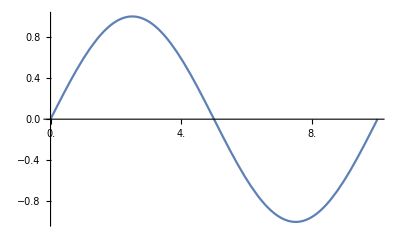

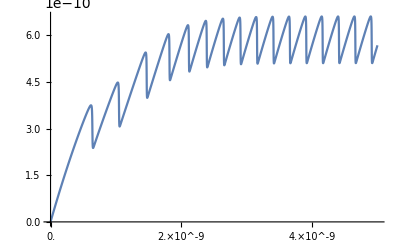

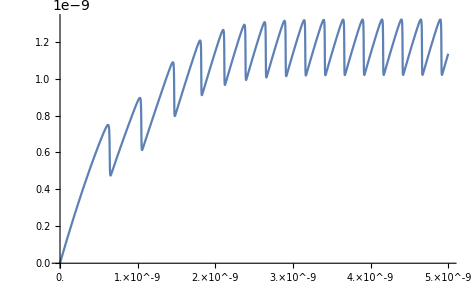

```mathematica
(*rescaling tics*)

Plot[Sin[200 Pi t],{t,0.,.01},Ticks->{{#,1000 #}&/@FindDivisions[{0.,.01},5]//N,Automatic}]

Plot[k(v t-Evaluate[p[t]/.s]),{t,0,tmax},PlotPoints->500,PlotRange->All,Ticks->{{#,v#}&/@FindDivisions[{0.0,tmax},5]//N,Automatic}]

ticks[min_,max_]:=Table[If[Mod[Round[i/a],4]==0,{i,i,{.02,0}},{i,"",{.01,0}}],{i,0,v tmax,a}]
(*ticks[min_,max_]:=Table[If[FractionalPart[i]==0.,{i,i,{.02,0}},{i,"",{.01,0}}],{i,Floor[min],Ceiling[max],0.1}]
Plot[2*Sin[p],{p,-π,π},Frame->True,FrameTicks->{ticks,ticks,False,False},Axes->True]*)
Plot[2k(v t-Evaluate[p[t]/.s]),{t,0,tmax},PlotPoints->500,PlotRange->All,Ticks->{ticks,Automatic,True,True}]
```

{5.67038×10^-11,1.26416×10^-10}

{5.67038×10^-9,1.26416×10^-10}

{{2.10962×10^-9,2.57963×10^-10},{3.20693×10^-9,2.60898×10^-10}}

FittedModel[2.52321×10^-10+0.0026745 t]

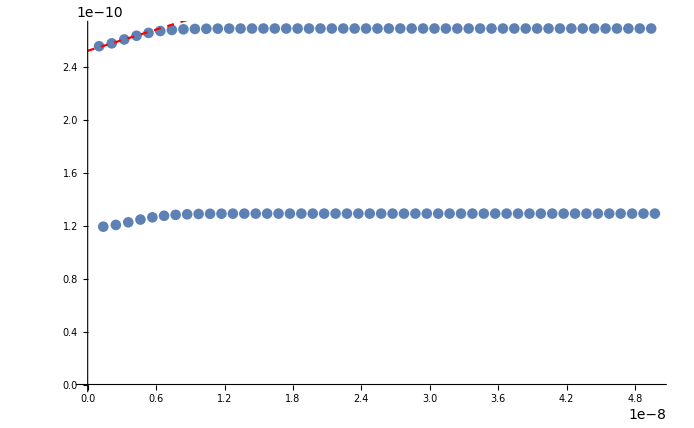

{{2.10962×10^-11,2.57963×10^-10},{3.20693×10^-11,2.60898×10^-10}}

FittedModel[2.52321×10^-10+0.26745 t]

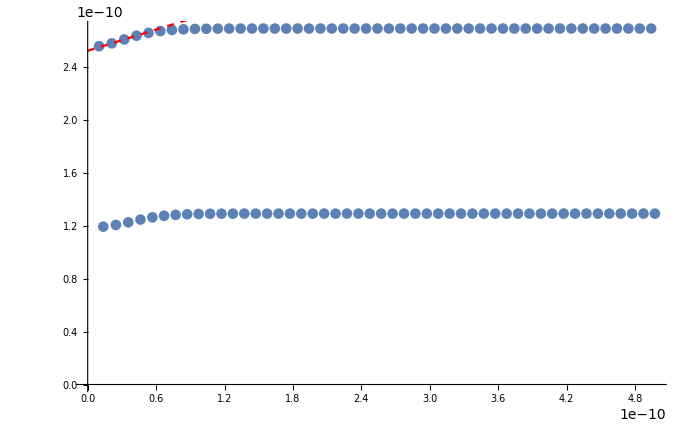

```mathematica
(*fitting to extrema*)

shiftextrema=Table[{extrema[[i]][[1]]*100,extrema[[i]][[2]]},{i,1,Length[extrema]}];
extrema[[10]]
shiftextrema[[10]]
tmp=ListPlot[shiftextrema];
maxdiff=Max[Table[shiftextrema[[i+2]][[2]]-shiftextrema[[i]][[2]],{i,1,Length[shiftextrema]-2}]];
tol= maxdiff-0.1maxdiff;
fitdata=Table[If[shiftextrema[[i+2]][[2]]-shiftextrema[[i]][[2]]>tol,shiftextrema[[i]],##&[]],{i,1,Length[shiftextrema]-2}]
fit=LinearModelFit[fitdata,t,t]
fitplot=Plot[fit[p],{p,0,100tmax/2},PlotStyle->{Red,Dashed}];
Show[tmp,fitplot]
tmp=ListPlot[extrema];
maxdiff=Max[Table[extrema[[i+2]][[2]]-extrema[[i]][[2]],{i,1,Length[extrema]-2}]];
tol= maxdiff-0.1maxdiff;
fitdata=Table[If[extrema[[i+2]][[2]]-extrema[[i]][[2]]>tol,extrema[[i]],##&[]],{i,1,Length[extrema]-2}]
fit=LinearModelFit[fitdata,t,t]
fitplot=Plot[fit[p],{p,0,tmax/2},PlotStyle->{Red,Dashed}];
Show[tmp,fitplot]
```

```mathematica
(*3d trijectories*)

(*1/2k(p[t]-v t)^2+(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-q[t])/a])+(c3 q[t]^4-c4 q[t]^2)*)

c1=3*^-20; (*3*^-20*)
c2=8/10*1*^-2; (*0.8*^-2*)
c3=5*^16; (*5*^16*)
a  =1*^-9;(*1*^-9*)

path=ParametricPlot3D[Evaluate[{p[t],q[t],(c1+c2 q[t]^2)(1-Cos[2Pi(p[t]-q[t])/a])+(c3 q[t]^4)}]/.s,{t,0,tmax/2.5},PlotPoints->100,PlotStyle->{Red},BoxRatios->{1, 1, 1},PlotRange->All,AxesLabel->{Style[p[t],Bold],Style[q[t],Bold],Style[V_qx + V_q,Bold]}]
pot=Plot3D[(c1+c2 q^2)(1-Cos[2Pi(p-q)/a])+(c3 q^4),{p,0,2.5*^-8},{q,0,1*^-9},PlotPoints->200,WorkingPrecision->100,BoxRatios->{1, 1, 1},AxesLabel->{Style[p[t],Bold],Style[q[t],Bold],Style[V_qx + V_q,Bold]},PlotStyle->None]
Show[path,pot]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*Finding force equilibration*)

Clear["Global`*"]

pot=(c1+c2 q^2)(1-Cos[2Pi(x-c4 q)/a])+(0+0 q^2)(1-Cos[c7 2Pi(x)/a])+c3 q^4
D[pot,q]
D[pot,x]
```

c3 q^4+(c1+c2 q^2) (1-Cos[(2 π (-c4 q+x))/a])

4 c3 q^3+2 c2 q (1-Cos[(2 π (-c4 q+x))/a])-(2 c4 π (c1+c2 q^2) Sin[(2 π (-c4 q+x))/a])/a

(2 π (c1+c2 q^2) Sin[(2 π (-c4 q+x))/a])/a

2.60021×10^-10

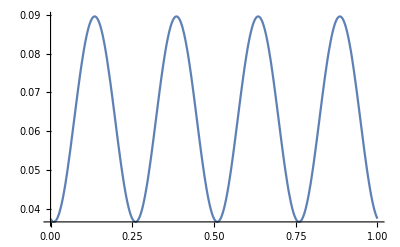

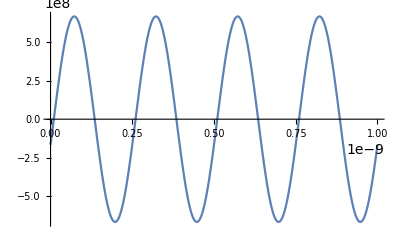

{4.75261×10^-9,4.77838×10^-10}

{4.97778×10^-9,6.57496×10^-10}

{4.72901×10^-9,2.48367×10^-10}

```mathematica
(*finding max q*)
qmax=Solve[4 c3 q^3+2 c2 q -(2 c4 π (c1+c2 q^2))/a==0,q];
qmax=Solve[4 c3 q^3+2 c2 q -(2 c4 π (c1+c2 q^2))/a==0,q][[3]][[1]][[2]]

Plot[c3 qmax^4+(c1+c2 qmax^2) (1-Cos[(2 π (-c4 qmax+x))/a]),{x,0,1*^-9}]
f[x_]=D[c3 qmax^4+(c1+c2 qmax^2) (1-Cos[(2 π (-c4 qmax+x))/a]),x];
Plot[f[x],{x,0,1*^-9}]


extrema[[Length@extrema-1]]
extrema[[Length@extrema-0]]
qextrema[[Length@qextrema-2]]
```

```mathematica
tmp=FullSimplify@Solve[4 cc3 q^3+2 cc2 q -(2 cc4 π (cc1+cc2 q^2))/aa==0,q][[1]][[1]][[2]];
FullSimplify[2Pi/aa(cc1+cc2 tmp^2)]
```

1/aa 2 π (cc1+cc2 ((cc2 cc4 π)/(6 aa cc3)+(cc2 (-6 aa^2 cc3+cc2 cc4^2 π^2))/(6 aa^2 cc3 (1/aa^3(-9 aa^2 cc3 (cc2^2-6 cc1 cc3) cc4 π+cc2^3 cc4^3 π^3+3 √3 aa^3 √(1/aa^4 cc3^2 (8 aa^4 cc2^3 cc3-aa^2 (cc2^4+36 cc1 cc2^2 cc3-108 cc1^2 cc3^2) cc4^2 π^2+4 cc1 cc2^3 cc4^4 π^4))))^(1/3))+1/(6 cc3)(1/aa^3(-9 aa^2 cc3 (cc2^2-6 cc1 cc3) cc4 π+cc2^3 cc4^3 π^3+3 √3 aa^3 √(1/aa^4 cc3^2 (8 aa^4 cc2^3 cc3-aa^2 (cc2^4+36 cc1 cc2^2 cc3-108 cc1^2 cc3^2) cc4^2 π^2+4 cc1 cc2^3 cc4^4 π^4))))^(1/3))^2)

```mathematica
Plot[1/a 2 π (c1+c2 ((c2 c4 π)/(6 a cc3)+(c2 (-6 a^2 cc3+c2 c4^2 π^2))/(6 a^2 cc3 (1/a^3(-9 a^2 cc3 (c2^2-6 c1 cc3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √(1/a^4 cc3^2 (8 a^4 c2^3 cc3-a^2 (c2^4+36 c1 c2^2 cc3-108 c1^2 cc3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))))^(1/3))+1/(6 cc3)(1/a^3(-9 a^2 cc3 (c2^2-6 c1 cc3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √(1/a^4 cc3^2 (8 a^4 c2^3 cc3-a^2 (c2^4+36 c1 c2^2 cc3-108 c1^2 cc3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))))^(1/3))^2),{cc3,0,20*^20}]
```

-Graphics-

```mathematica
(*Finding force equilibration*)

Clear["Global`*"]

pot=(c1+c2 q^2)(1-Cos[2Pi(x-c4 q)/a])+(0+0 q^2)(1-Cos[c7 2Pi(x)/a])+c3 q^2
D[pot,q]
D[pot,x]
```

c3 q^2+(c1+c2 q^2) (1-Cos[(2 π (-c4 q+x))/a])

2 c3 q+2 c2 q (1-Cos[(2 π (-c4 q+x))/a])-(2 c4 π (c1+c2 q^2) Sin[(2 π (-c4 q+x))/a])/a

(2 π (c1+c2 q^2) Sin[(2 π (-c4 q+x))/a])/a

```mathematica
(*finding max q*)
qmax=Solve[2c3 q+2 c2 q -(2 c4 π (c1+c2 q^2))/a==0,q];
qmax=Solve[ 2c3 q+2 c2 q -(2 c4 π (c1+c2 q^2))/a==0,q][[3]][[1]][[2]]

Plot[c3 qmax^4+(c1+c2 qmax^2) (1-Cos[(2 π (-c4 qmax+x))/a]),{x,0,1*^-9}]
f[x_]=D[c3 qmax^4+(c1+c2 qmax^2) (1-Cos[(2 π (-c4 qmax+x))/a]),x];
Plot[f[x],{x,0,1*^-9}]


extrema[[Length@extrema-1]]
extrema[[Length@extrema-0]]
qextrema[[Length@qextrema-2]]
```

```mathematica
tmp=Solve[2 cc3 q+2 cc2 q -(2 cc4 π (cc1+cc2 q^2))/aa==0,q]
```

{{q→-(aa (-2 cc2-2 cc3-√((2 cc2+2 cc3)^2-(16 cc1 cc2 cc4^2 π^2)/aa^2)))/(4 cc2 cc4 π)},{q→-(aa (-2 cc2-2 cc3+√((2 cc2+2 cc3)^2-(16 cc1 cc2 cc4^2 π^2)/aa^2)))/(4 cc2 cc4 π)}}

-(aa (-2 cc2-2 cc3+√((2 cc2+2 cc3)^2-(16 cc1 cc2 cc4^2 π^2)/aa^2)))/(4 cc2 cc4 π)

(aa (cc2+cc3) (cc2+cc3-√((cc2+cc3)^2-(4 cc1 cc2 cc4^2 π^2)/aa^2)))/(cc2 cc4^2 π)

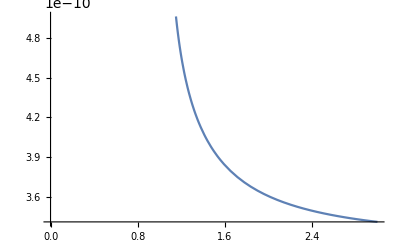

```mathematica
tmp=Solve[2 cc3 q+2 cc2 q -(2 cc4 π (cc1+cc2 q^2))/aa==0,q][[2]][[1]][[2]]
FullSimplify[2Pi/aa(cc1+cc2 tmp^2)]
Plot[(a (c2+cc3) (c2+cc3-√((c2+cc3)^2-(4 c1 c2 c4^2 π^2)/a^2)))/(c2 c4^2 π),{cc3,0,3}]
```

```mathematica
(a (c2+cc3) (c2+cc3-√((c2+cc3)^2-(4 c1 c2 c4^2 π^2)/a^2)))/(c2 c4^2 π)
```

5.41343×10^-13 (3.+cc3) (3.+cc3-√(-3714.13+(3.+cc3)^2))

```mathematica
β cc3^2-√(α+cc3+cc3^2)
β cc3 (c2+cc3-√(α+cc3+cc3^2))
β cc3 (c2+cc3-√(α+cc3+(c2+cc3)^2))
```

-√(cc3+cc3^2+α)+cc3^2 β

cc3 (3.+cc3-√(cc3+cc3^2+α)) β

cc3 (3.+cc3-√(cc3+(3.+cc3)^2+α)) β

```mathematica
αα=-(4 c1 c2 c4^2 π^2)/a^2
ββ=a/(c2 c4^2 π)
Manipulate[{(a (c2+cc3) (c2+cc3-√((c2+cc3)^2-(4 c1 c2 c4^2 π^2)/a^2)))/(c2 c4^2 π),
ββ(cc3-√(αα+cc3^2)),
ββ cc3(cc3-√(αα+cc3^2)),
ββ cc3 (c2+cc3-√(αα+cc3^2)),
ββ (cc3+c2) (c2+cc3-√(αα+cc3^2)),
ββ cc3 (c2+cc3-√(αα+cc3+cc3^2)),
ββ cc3 (c2+cc3-√(αα+(c2+cc3)^2))},{cc3,0,3}]
```

-1.6423

3.97887×10^-10

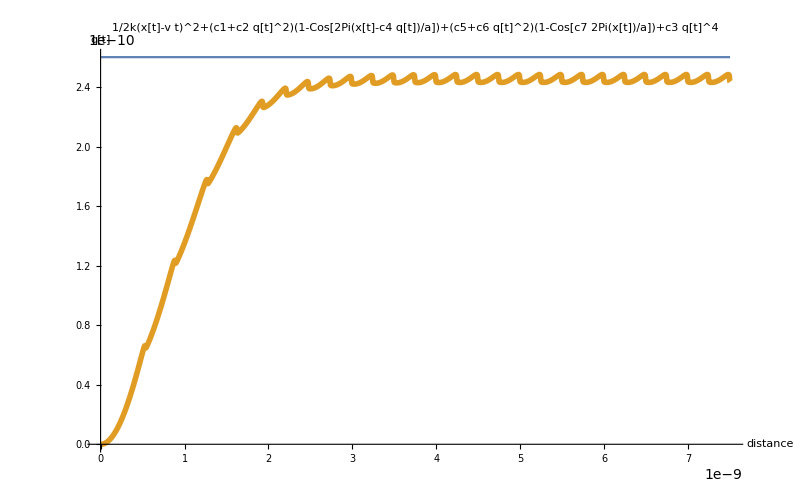

```mathematica
qimg = ParametricPlot[{v t,Evaluate[q[t]/.s]},{t,0,tmax},PlotPoints->500,PlotRange->All,PlotLabel->anpotstring,ImageSize->800,AspectRatio->1/GoldenRatio,AxesLabel->{"distance","q[t]"},PlotStyle->Thickness[0.005]];
tmpimg=Plot[2.600206485316246*^-10,{t,0,tmax}];
Show[qimg,tmpimg]
```

```mathematica
anqmax=FullSimplify@Solve[4 c3 q^3+2 c2 q -(2 c4 π (c1+c2 q^2))/a==0,q][[1]][[1]][[2]]
FullSimplify@D[(c1+c2 anqmax^2)(1-Cos[2Pi/a(p-c4 anqmax)])+c3 anqmax^4,p]
```

(c2 c4 π)/(6 a c3)+(c2 (-6 a^2 c3+c2 c4^2 π^2))/(6 a^2 c3 ((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))+(((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))/(6 c3)

1/a 2 π (c1+c2 ((c2 c4 π)/(6 a c3)+(c2 (-6 a^2 c3+c2 c4^2 π^2))/(6 a^2 c3 ((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))+(((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))/(6 c3))^2) Sin[1/a 2 π (p-c4 ((c2 c4 π)/(6 a c3)+(c2 (-6 a^2 c3+c2 c4^2 π^2))/(6 a^2 c3 ((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))+(((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))/(6 c3)))]

```mathematica
1/a 2 π (c1+c2 ((c2 c4 π)/(6 a c3)+(c2 (-6 a^2 c3+c2 c4^2 π^2))/(6 a^2 c3 ((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))+(((-9 a^2 c3 (c2^2-6 c1 c3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √((c3^2 (8 a^4 c2^3 c3-a^2 (c2^4+36 c1 c2^2 c3-108 c1^2 c3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))/a^4))/a^3)^(1/3))/(6 c3))^2)
```

6.66574×10^-10

```mathematica
s1=First[p/.NDSolve[{-mp p''[t]-D[anpot,p[t]]-mp ηp (p'[t])==0,-mq q''[t]-D[anpot,q[t]]-mq ηq(q'[t])==0,p[0]==0,p'[0]==0,q[0]==0,q'[0]==0},{p,q},{t,tmax/2,tmax},MaxSteps->1000000,Method->{"StiffnessSwitching"}] (*,Method->{"StiffnessSwitching"} AccuracyGoal->∞, "TimeIntegration"-> *)]
s1[7.2258*^-9]
```

-9        -9
InterpolatingFunction[{{3.75 10  , 7.5 10  }}, <>]

6.57×10^-9

-6.25×10^-11+p

{{q→0.-2.54951×10^-10 ⅈ},{q→0.+2.54951×10^-10 ⅈ}}

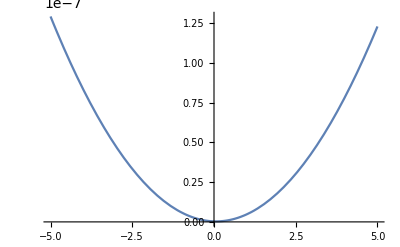

{3.26726×10^-10,{p→6.25938×10^-11}}

```mathematica
(*playing around with dV/dx = 0*)
q0=(p-a/4)/c4
Solve[(2 π (c1+c2 q^2))/a==0,q]
Plot[(2 π (c1+c2 ((p-a/4)/c4)^2))/a,{p,-5*^-9,5*^-9}]
FindMinimum[(2 π (c1+c2 ((p-a/4)/c4)^2))/a,{p,1*^-9}]
```

```mathematica
Solve[4 c3 q^3+2 c2 q -(2 c4 π (c1+c2 q^2))/a==0,q]
```

{{q→-5.14705×10^-11-1.91357×10^-10 ⅈ},{q→-5.14705×10^-11+1.91357×10^-10 ⅈ},{q→2.60021×10^-10}}

{{3.98819×10^-9,6.64754×10^-10},{4.23819×10^-9,6.64754×10^-10},{4.48819×10^-9,6.64754×10^-10},{4.73819×10^-9,6.64754×10^-10},{4.98819×10^-9,6.64754×10^-10}}

FittedModel[6.64754×10^-10+1.03024×10^-8 t]

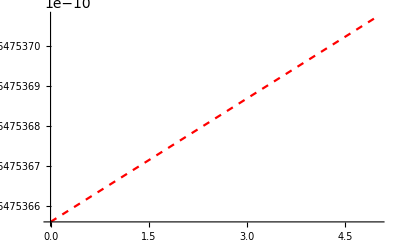

```mathematica
(*trying out the fitting for extrema*)

flatfitdata=Table[extrema[[2i]],{i,Length[extrema]/2-4,Length[extrema]/2}]
flatfit=LinearModelFit[flatfitdata,t,t]
flatfitplot=Plot[flatfit[p],{p,0,tmax},PlotStyle->{Red,Dashed}]
```

```mathematica
(*playing around with data visualization*)
GetRLine3[MMStdata_,IO_: 1][p_: p]:=ListInterpolation[#,InterpolationOrder->IO,Method->"Spline"][p]&/@(({{#[[1]]},#[[2]]})&/@#&/@MMStdata);
data=Transpose[{#+RandomReal[]*0.1&/@Range[-10,30,0.4],Tanh[#]+(Sech[2 p-0.5]/1.5+1.5)/.p->#&/@Range[-4,4,0.08]}];

xLimits={Min@#1,Max@#1}&@@Transpose[data];
f=First[100*D[GetRLine3[{data},3][p],p]];

vals=Reap[soln=y[p]/.First[NDSolve[{y'[p]==Evaluate[D[f,p]],y[-9.9]==(f/.p->-9.9)},y[p],{p,-9.9,30},Method->{"EventLocator","Event"->y'[p],"EventAction":>Sow[{p,y[p]}]}]]][[2,1]];

Plot[f,{p,-9.9,30},Epilog->{PointSize[Medium],Red,Point[vals]}]
```

NDSolve::ndsz: At t == 0.445051, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 5.73111×10^13 at t = 0.445051 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[{{…, 0., 1., …}, {0., 0.445051}}, <>]

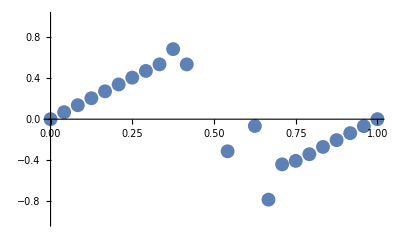

-Graphics3D-

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
mdfun=First[u/.NDSolve[{D[u[p,t],t]==0.01 D[u[p,t],p,p]-u[p,t] D[u[p,t],p],u[0,t]==u[1,t],u[p,0]==Sin[2 Pi p]},u,{p,0,1},{t,0,0.5}]]
end=InterpolatingFunctionDomain[mdfun][[2,-1]];
p=InterpolatingFunctionCoordinates[mdfun][[1]];
ListPlot[Transpose[{p,mdfun[p,end]}],PlotStyle->PointSize[.025],PlotRange->{-1,1}]
Show[Graphics3D[{Map[Line,MapThread[Append,{InterpolatingFunctionGrid[mdfun],InterpolatingFunctionValuesOnGrid[mdfun]},2]],{RGBColor[1,0,0],Line[Transpose[{p,0. p,mdfun[p,0.]}]]}}],BoxRatios->{1,1,1},PlotRange->{All,All,{-1,1}}]
```

```mathematica
(*some old obsolete stuff?*)
k = 1;
v = 200;
V0 = 0.75*^-19;
a = 1*^-9;
m = 1*^-25;
η = 6.5*^12;
tmax=50000*1*^-15;
s=NDSolve[{-m p''[t]-(2 π V0 Sin[(2 π p[t])/a])/a-k (-t v+p[t])-m η(p'[t])==0,p[0]==0,p'[0]==0},{p},{t,0,tmax},MaxSteps->100000]
Plot[k(v t-Evaluate[p[t]/.s]),{t,0,tmax},PlotRange->All]
```

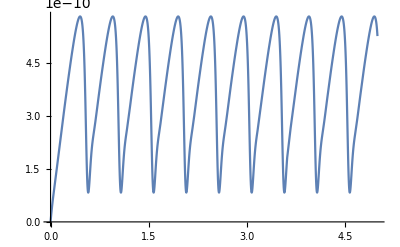

```mathematica
{{p->                                 -11
InterpolatingFunction[{{0., 5. 10   }}, <>]}}
```

```mathematica
(*also old obsolete stuff?*)
p[1*^-15]==9.97834*^-19
Sin[2Pi p[t]/a]
+pf Sin[2Pi p[t]/a]
pf Log[p[t]] (*pf = 4*^14, η = 50*^12*)
```

```mathematica
Manipulate[1/2k(p-v t)^2+V0(1-Cos[(2Pi/a)p]),{k,0,10},{p,0,1*^-6},{v,0,1*^-6},{t,0,1*^-10},{V0,0,1*^-9},{a,0,1*^-8}]
```

```mathematica
k = 1;
x0 = 1.35*^-9;
v0 = 1*^-7;
t0 = 0;
V0 = 1*^-18;
a = 1*^-9;
m = 1*^-26;
η = 1*^-17;
vel0 = 0;

1/2k(x0-v0 t0)^2+V0(1-Cos[2Pi x0/a])
-k(x0-v0 t0)/m-2V0 Pi/(m a) Sin[2Pi x0/a]-η vel0
```

2.49904×10^-18

-6.4332×10^17

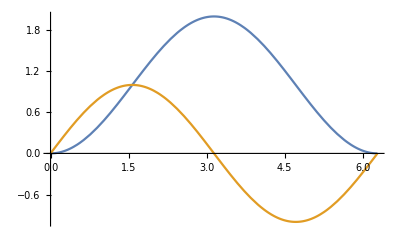

```mathematica
(*sanity check*)
Plot[{1-Cos[p],Sin[p]},{p,0,2Pi}]
```

```mathematica
52*(1-(0.015*1.40))^30
Reduce[52*(0.985)^x==40,x]
```

27.5096

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈Integers&&x==17.3594-(0.+415.73 ⅈ) C[1]

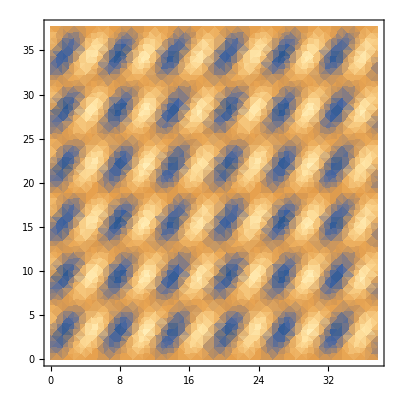

```mathematica
DensityPlot[Sin[x-y]-Sin[x],{x,0,12Pi},{y,0,12Pi},GridLines->{{4.5Pi,5.5Pi},{4Pi,5Pi}},Method->{"GridLinesInFront"->True}]
```

```mathematica
(*number of words PRL*)
```

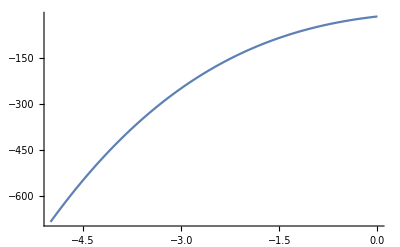

```mathematica
ParametricPlot[{k,2 (k-2)^3},{k,-5,0},PlotRange->All,AspectRatio->1/GoldenRatio]
```

ParametricPlot::sclfn: -- Message text not found -- ({{-#1&,-#1&},{-#1&,-#1&}})

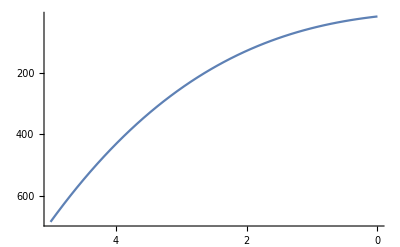

```mathematica
ParametricPlot[{k,2 (k-2)^3},{k,-5,0},ScalingFunctions->{{-#&,-#&},{-#&,-#&}},PlotRange->All,AspectRatio->1/GoldenRatio]
```

FittedModel[1.14303 x (x-√Abs[-1.01591+x^2])]

NonlinearModelFit::nrlnum: The function value {-0.000122085+0.000122055 ⅈ,-0.264102+0.0000654173 ⅈ,-0.0352814+0.0000628319 ⅈ,0.0580666+0.0000620199 ⅈ} is not a list of real numbers with dimensions {4} at {α,β} = {1.,1.}.

FittedModel[1. x (x-√Abs[-1.+x^2])]

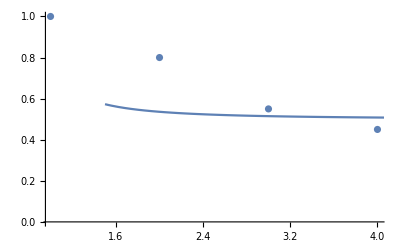

```mathematica
list1={{1,1.0},{2,0.8},{3,0.65},{4,0.45}};
(*Substrate effect on thickness dependent friction on graphene*)
list2={{1,0.9/0.9},{2,0.7/0.9},{3,0.55/0.9}};
(*Role of wrinkle height in friction variation with number of graphene layers*)
list3={{1,1.0},{2,0.80},{3,0.55},{4,0.45}};
(*Frictional Characteristics of Atomically Thin Sheets*)


(*nlm1=NonlinearModelFit[list1,α x(x-√(β+x^2))+0,{α,β,γ},x]
nlm2=NonlinearModelFit[list2,α x(x-√(β+x^2))+0,{α,β,γ},x]*)
nlm3=NonlinearModelFit[list3,α x(x-√Abs[-β+x^2])+0,{α,β,γ},x]
nlm3=NonlinearModelFit[list3,1/(1-√(-β+1)) x(x-√Abs[-β+x^2]),{α,β},x]

Show[ListPlot[list3],Plot[nlm3[x],{x,1.5,4.5}]]

(*,Gradient->"FiniteDifference"*)
```

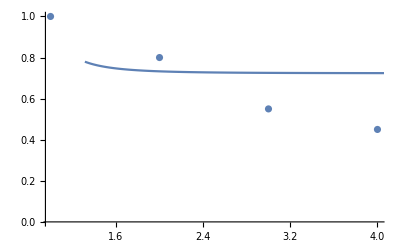

```mathematica
ββ=0.8;
Show[ListPlot[list3],Plot[1/(1-√(-ββ+1)) x^2(x^2-√(-ββ+x^4)),{x,1.0,4.5}]]
```

```mathematica
^
```

```mathematica
Plot[1/a 2 π (c1+c2 ((c2 c4 π)/(6 a cc3)+(c2 (-6 a^2 cc3+c2 c4^2 π^2))/(6 a^2 cc3 (1/a^3(-9 a^2 cc3 (c2^2-6 c1 cc3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √(1/a^4 cc3^2 (8 a^4 c2^3 cc3-a^2 (c2^4+36 c1 c2^2 cc3-108 c1^2 cc3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))))^(1/3))+1/(6 cc3)(1/a^3(-9 a^2 cc3 (c2^2-6 c1 cc3) c4 π+c2^3 c4^3 π^3+3 √3 a^3 √(1/a^4 cc3^2 (8 a^4 c2^3 cc3-a^2 (c2^4+36 c1 c2^2 cc3-108 c1^2 cc3^2) c4^2 π^2+4 c1 c2^3 c4^4 π^4))))^(1/3))^2),{cc3,1*^18,100*^18}]
```

-Graphics-

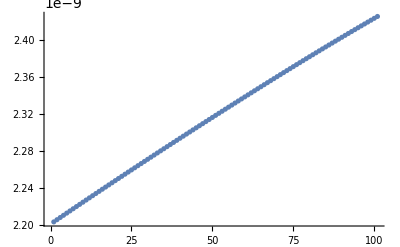

```mathematica
scale=1*^-9;
frics=ToExpression@Flatten@Import["../code/fric_out.dat"];
ListPlot[frics]
```